# Subspace recompilation for BCS Hamiltonian

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]*)
(*SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_gpu"];*)
```

### Modules

```mathematica
GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
};
```

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire BCS Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

Constants

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0];
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0];
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0];
```

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs;
```

initial states and memory allocation

```mathematica
DestroyAllQuregs[]
{ψexact,ψinitexact}=CreateQuregs[5,2];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

## Obtain the expression ⅇ^(-i δt H_BCS)

```mathematica
(* Medium resolution *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20.,0.2],{20.,23.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

True

```mathematica
Length@τs
```

65

The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
(*τ=t J/ℏ*)
```

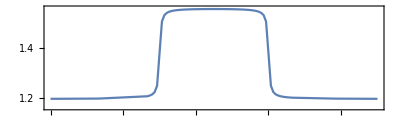

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

```mathematica
rexactot2<<rexactot2.mx
```

Null rexactot2

Rerun big numbers of native gates > 100

```mathematica
bcscompilecssrerun={};
```

0.

**** Compile @Wed 28 Dec 2022 05:07:29 τ=0.; δ0.2 ****

τ=0.2; δ=0.2; cost=5.31797×10^-6; ngates=37; runtime=14.147 min

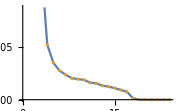

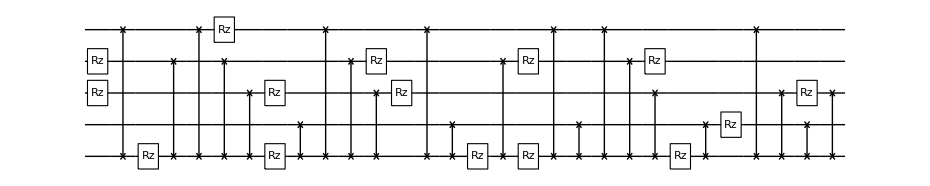

**** Compile @Wed 28 Dec 2022 05:21:38 τ=0.2; δ0.2 ****

τ=0.4; δ=0.2; cost=5.46442×10^-6; ngates=40; runtime=5.9901 min

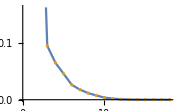

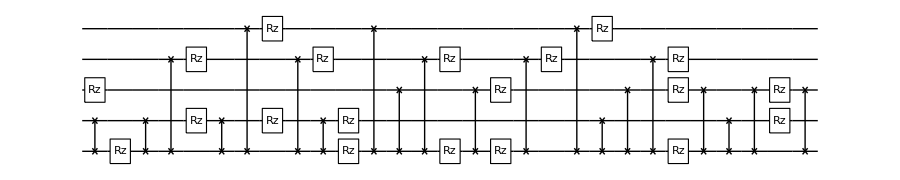

**** Compile @Wed 28 Dec 2022 05:27:43 τ=0.4; δ0.2 ****

τ=0.6; δ=0.2; cost=5.76855×10^-6; ngates=40; runtime=10.2954 min

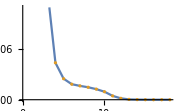

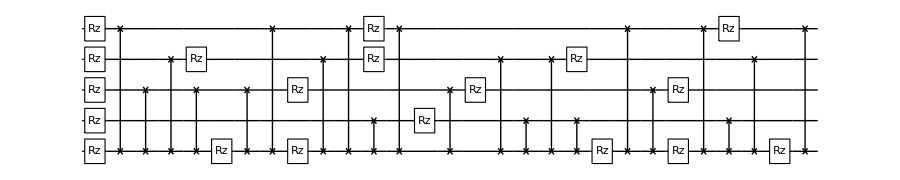

**** Compile @Wed 28 Dec 2022 05:38:07 τ=0.6; δ0.2 ****

τ=0.8; δ=0.2; cost=6.5167×10^-6; ngates=44; runtime=6.50079 min

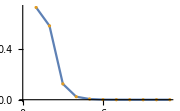

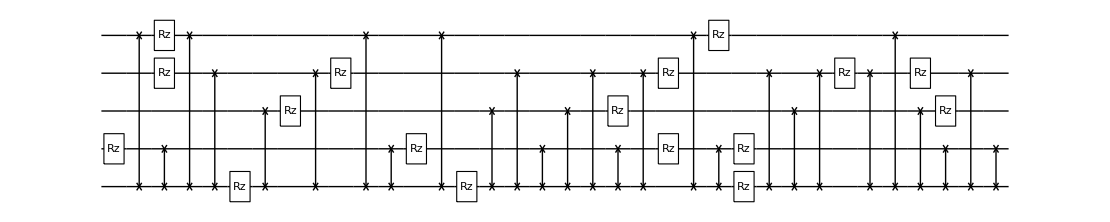

**** Compile @Wed 28 Dec 2022 05:44:43 τ=0.8; δ0.2 ****

τ=1.; δ=0.2; cost=3.0106×10^-6; ngates=38; runtime=7.79456 min

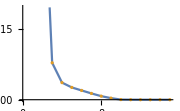

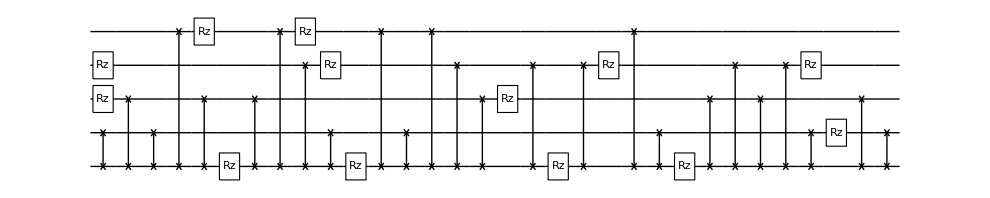

**** Compile @Wed 28 Dec 2022 05:52:37 τ=1.; δ0.2 ****

τ=1.2; δ=0.2; cost=4.26854×10^-6; ngates=45; runtime=5.79031 min

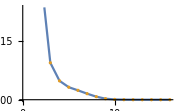

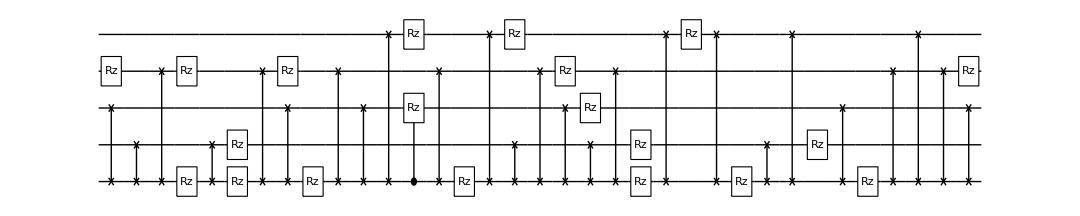

**** Compile @Wed 28 Dec 2022 05:58:30 τ=1.2; δ0.2 ****

τ=1.4; δ=0.2; cost=3.78367×10^-6; ngates=48; runtime=9.61929 min

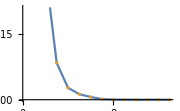

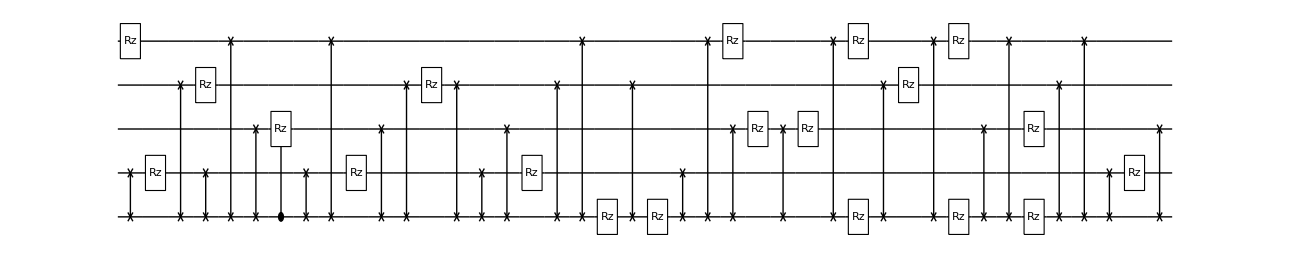

**** Compile @Wed 28 Dec 2022 06:08:14 τ=1.4; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 06:21:52 completed with ngates=42, cost=6.0053940371673775e-6, at eval=2003

τ=1.6; δ=0.2; cost=4.95116×10^-6; ngates=42; runtime=14.7881 min

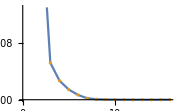

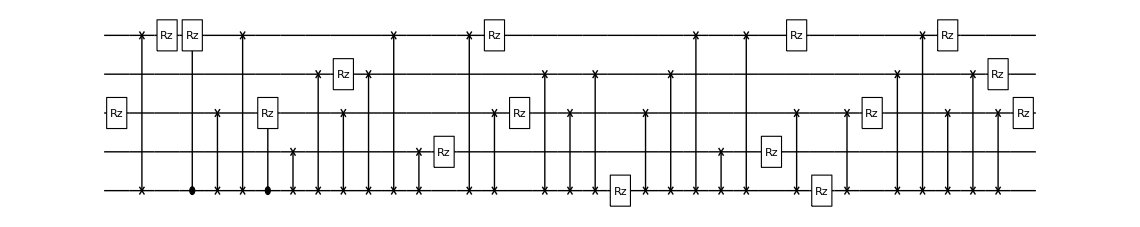

**** Compile @Wed 28 Dec 2022 06:23:07 τ=1.6; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 06:37:34 completed with ngates=45, cost=4.009292699280742e-6, at eval=2114

τ=1.8; δ=0.2; cost=4.00929×10^-6; ngates=45; runtime=16.2744 min

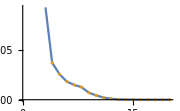

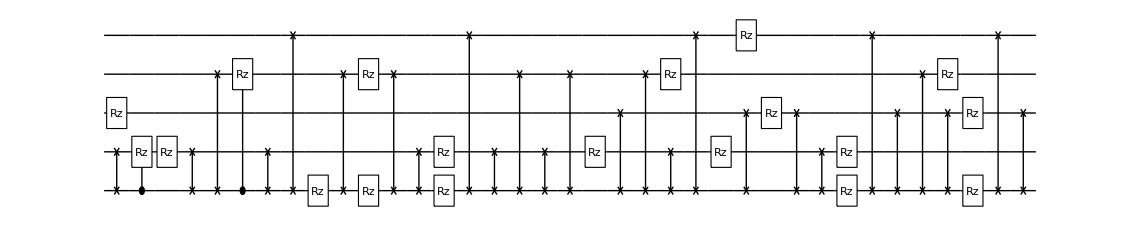

**** Compile @Wed 28 Dec 2022 06:39:29 τ=1.8; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 06:53:23 completed with ngates=37, cost=8.66396790510926e-6, at eval=2375

τ=2.; δ=0.2; cost=6.127×10^-6; ngates=37; runtime=14.7359 min

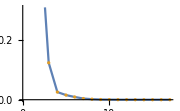

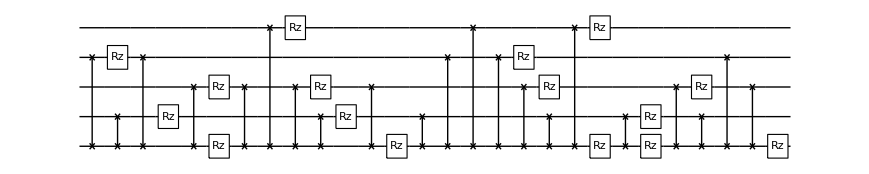

**** Compile @Wed 28 Dec 2022 06:54:20 τ=2.; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 07:08:19 completed with ngates=44, cost=0.000010568759829965302, at eval=2094

τ=2.2; δ=0.2; cost=6.76308×10^-6; ngates=44; runtime=15.3089 min

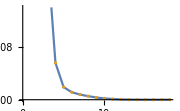

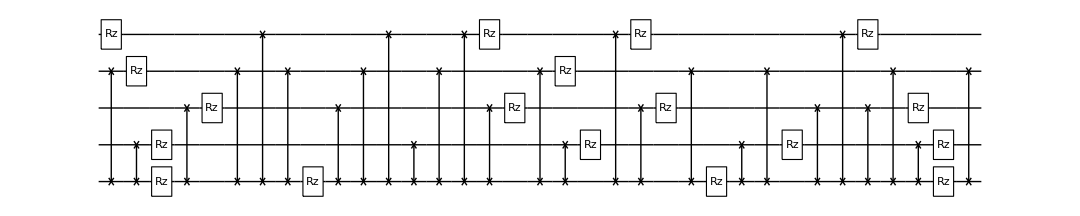

**** Compile @Wed 28 Dec 2022 07:09:44 τ=2.2; δ0.2 ****

τ=2.4; δ=0.2; cost=5.67708×10^-6; ngates=45; runtime=17.1076 min

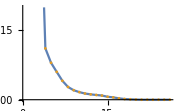

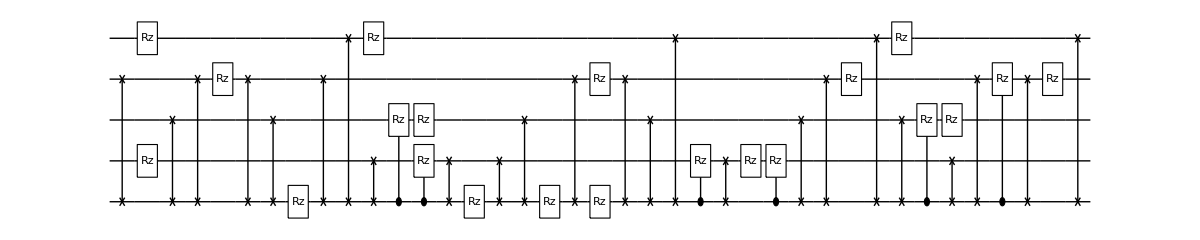

**** Compile @Wed 28 Dec 2022 07:26:57 τ=2.4; δ0.2 ****

τ=2.6; δ=0.2; cost=1.41811×10^-6; ngates=42; runtime=7.12249 min

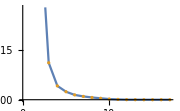

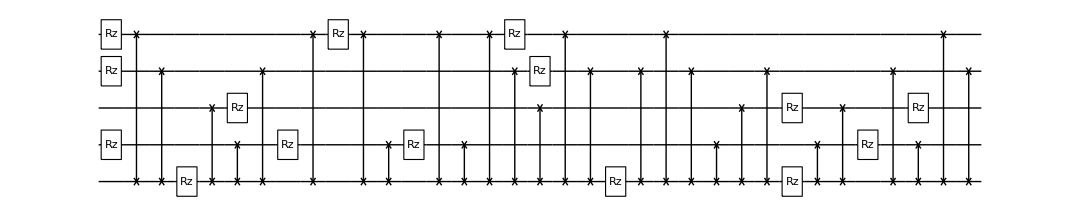

**** Compile @Wed 28 Dec 2022 07:34:10 τ=2.6; δ0.2 ****

τ=2.8; δ=0.2; cost=9.98564×10^-6; ngates=38; runtime=9.07371 min

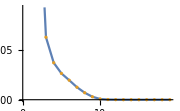

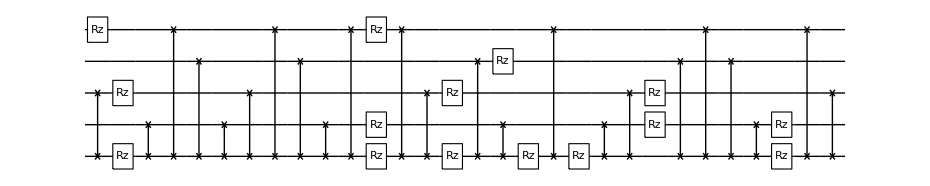

**** Compile @Wed 28 Dec 2022 07:43:21 τ=2.8; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 07:58:38 completed with ngates=43, cost=4.825350140791329e-6, at eval=2387

τ=3.; δ=0.2; cost=2.60437×10^-6; ngates=43; runtime=16.4625 min

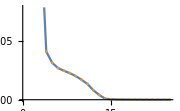

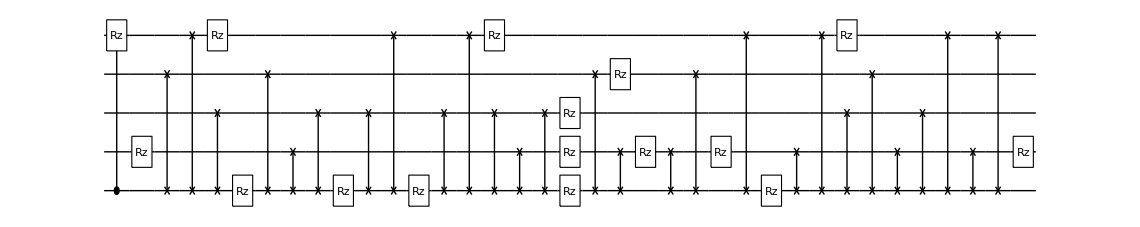

**** Compile @Wed 28 Dec 2022 07:59:55 τ=3.; δ0.2 ****

τ=3.2; δ=0.2; cost=4.66633×10^-6; ngates=35; runtime=13.5172 min

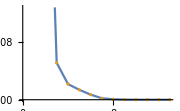

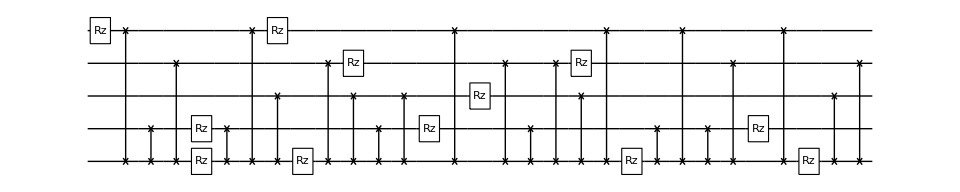

**** Compile @Wed 28 Dec 2022 08:13:32 τ=3.2; δ0.2 ****

τ=3.4; δ=0.2; cost=2.73887×10^-6; ngates=43; runtime=4.41217 min

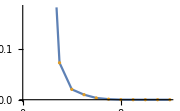

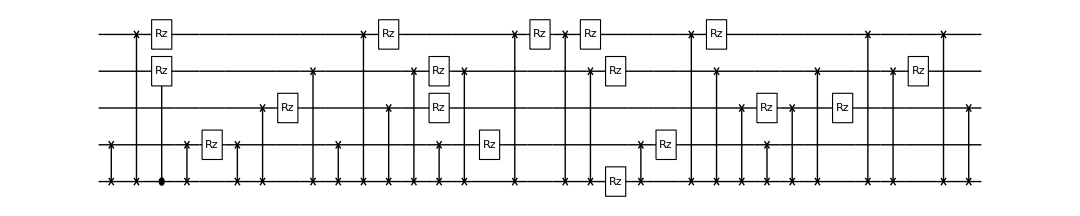

**** Compile @Wed 28 Dec 2022 08:18:03 τ=3.4; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 08:31:50 completed with ngates=38, cost=6.256683983574263e-6, at eval=2203

τ=3.6; δ=0.2; cost=2.98744×10^-6; ngates=38; runtime=14.992 min

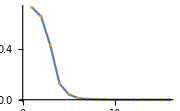

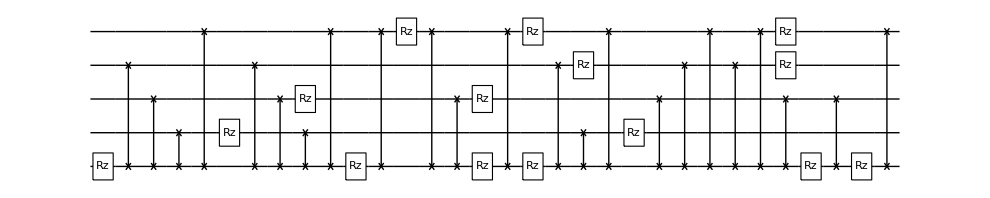

**** Compile @Wed 28 Dec 2022 08:33:08 τ=3.6; δ0.2 ****

τ=3.8; δ=0.2; cost=9.05287×10^-6; ngates=47; runtime=6.00107 min

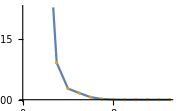

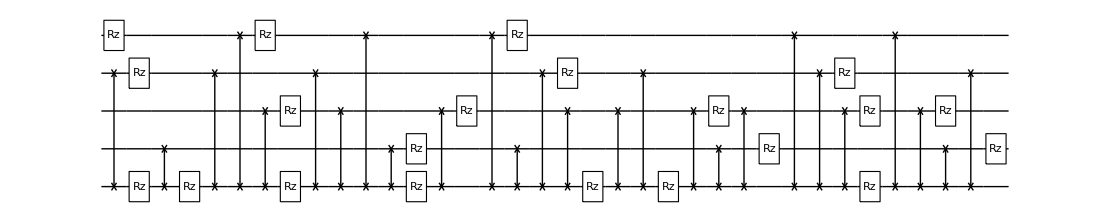

**** Compile @Wed 28 Dec 2022 08:39:14 τ=3.8; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 08:54:35 completed with ngates=35, cost=6.709691097395165e-6, at eval=2590

τ=4.; δ=0.2; cost=2.84444×10^-6; ngates=35; runtime=16.4337 min

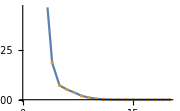

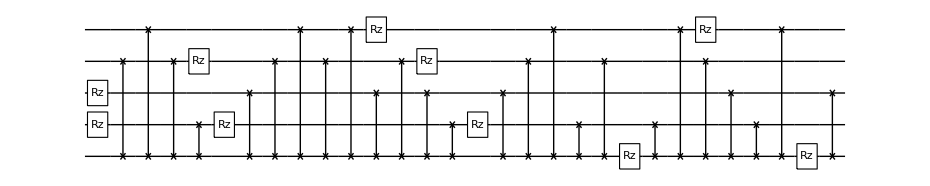

**** Compile @Wed 28 Dec 2022 08:55:47 τ=4.; δ0.2 ****

τ=4.2; δ=0.2; cost=5.62312×10^-6; ngates=45; runtime=8.07167 min

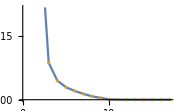

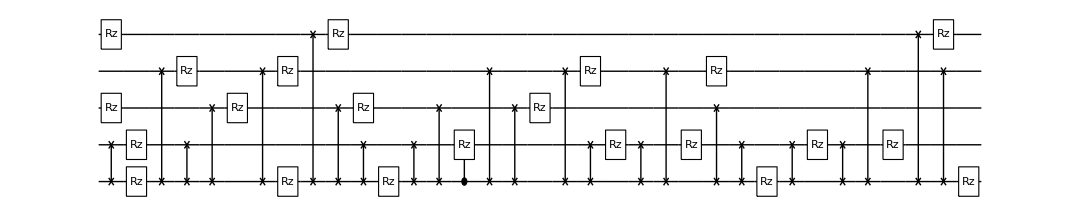

**** Compile @Wed 28 Dec 2022 09:03:57 τ=4.2; δ0.2 ****

τ=4.4; δ=0.2; cost=3.61311×10^-6; ngates=45; runtime=8.03422 min

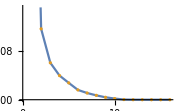

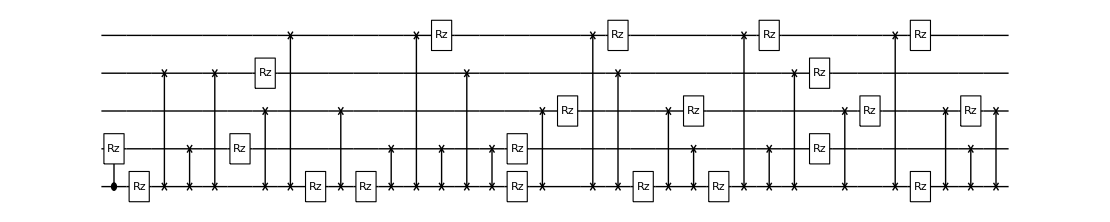

**** Compile @Wed 28 Dec 2022 09:12:05 τ=4.4; δ0.2 ****

τ=4.6; δ=0.2; cost=7.51931×10^-6; ngates=39; runtime=7.83936 min

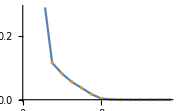

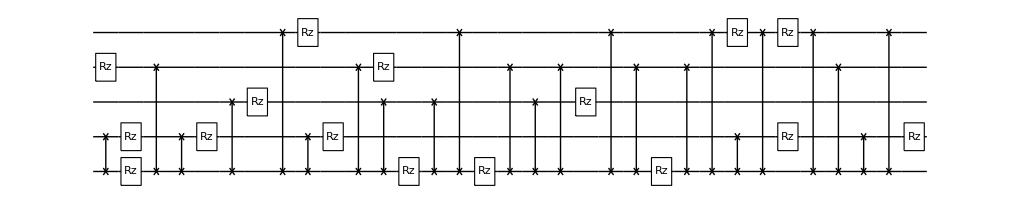

**** Compile @Wed 28 Dec 2022 09:20:02 τ=4.6; δ0.2 ****

τ=4.8; δ=0.2; cost=1.82924×10^-6; ngates=47; runtime=10.9945 min

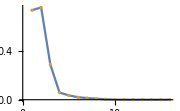

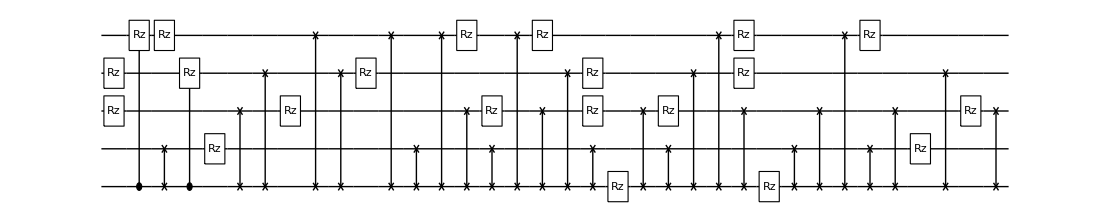

**** Compile @Wed 28 Dec 2022 09:31:08 τ=4.8; δ0.2 ****

τ=5.; δ=0.2; cost=3.76626×10^-6; ngates=43; runtime=9.79397 min

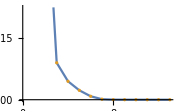

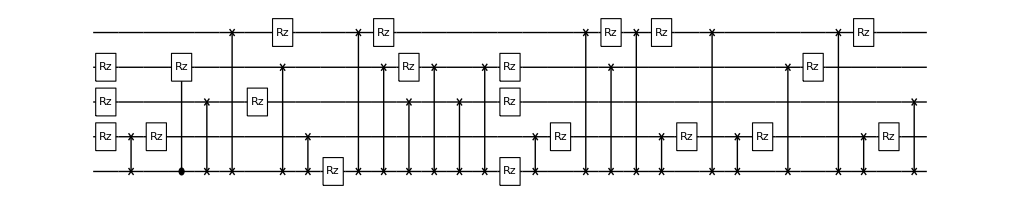

**** Compile @Wed 28 Dec 2022 09:41:01 τ=5.; δ0.2 ****

τ=5.2; δ=0.2; cost=9.61816×10^-6; ngates=41; runtime=11.4003 min

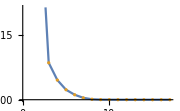

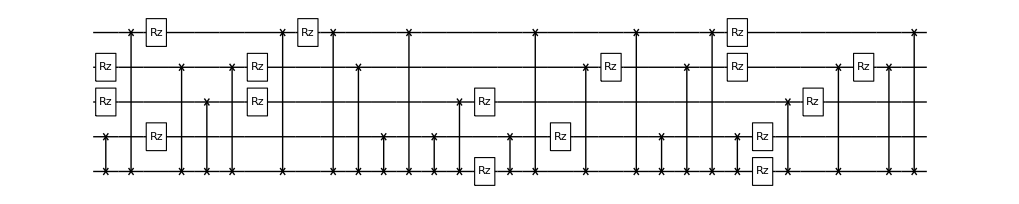

**** Compile @Wed 28 Dec 2022 09:52:31 τ=5.2; δ0.2 ****

τ=5.4; δ=0.2; cost=5.83649×10^-6; ngates=39; runtime=3.97417 min

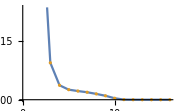

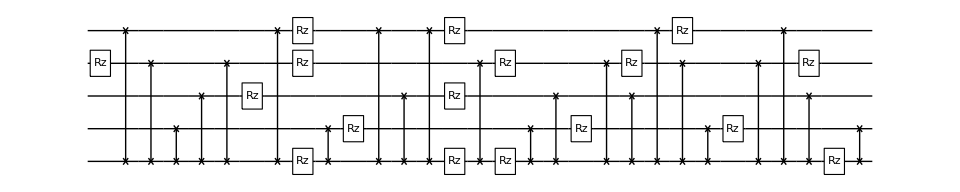

**** Compile @Wed 28 Dec 2022 09:56:36 τ=5.4; δ0.2 ****

τ=5.6; δ=0.2; cost=2.57079×10^-6; ngates=41; runtime=6.80598 min

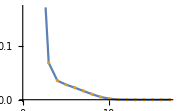

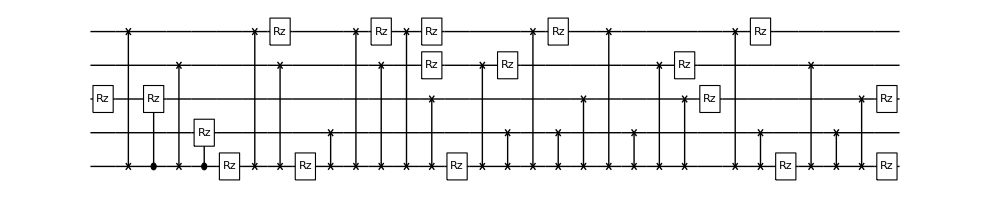

**** Compile @Wed 28 Dec 2022 10:03:30 τ=5.6; δ0.2 ****

τ=5.8; δ=0.2; cost=5.95507×10^-6; ngates=44; runtime=9.58671 min

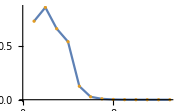

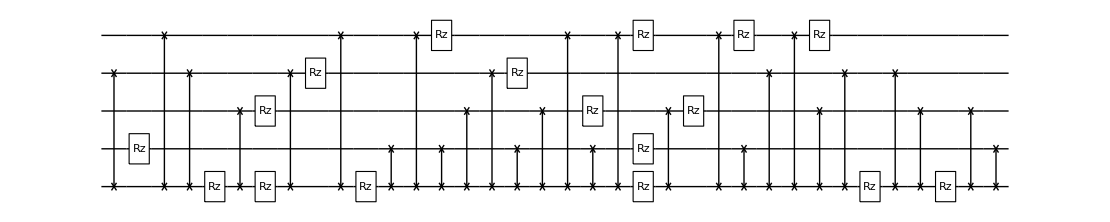

**** Compile @Wed 28 Dec 2022 10:13:12 τ=5.8; δ0.2 ****

τ=6.; δ=0.2; cost=3.41202×10^-6; ngates=41; runtime=13.5555 min

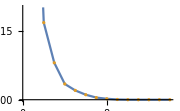

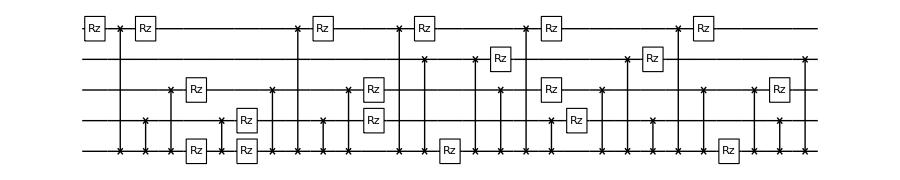

**** Compile @Wed 28 Dec 2022 10:26:51 τ=6.; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 10:40:13 completed with ngates=41, cost=0.000011163860066165654, at eval=1966

τ=6.2; δ=0.2; cost=5.70967×10^-6; ngates=41; runtime=14.5518 min

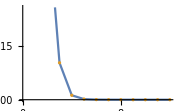

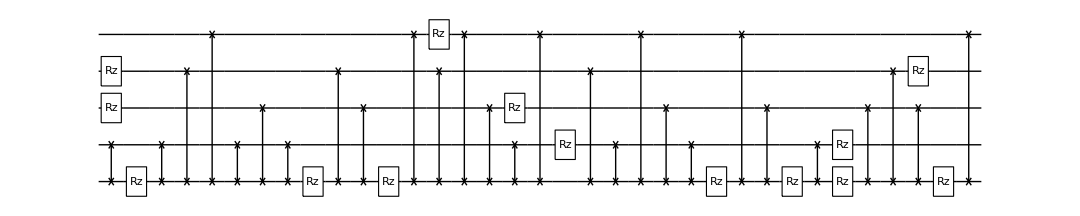

**** Compile @Wed 28 Dec 2022 10:41:30 τ=6.2; δ0.2 ****

τ=6.4; δ=0.2; cost=6.05855×10^-6; ngates=42; runtime=4.81649 min

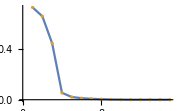

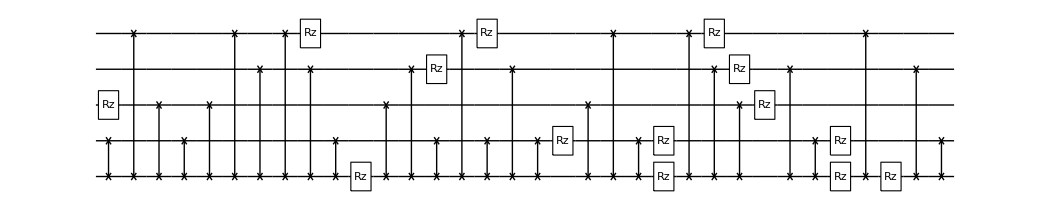

**** Compile @Wed 28 Dec 2022 10:46:25 τ=6.4; δ0.2 ****

τ=6.6; δ=0.2; cost=9.92577×10^-6; ngates=45; runtime=8.61613 min

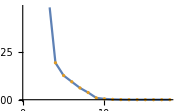

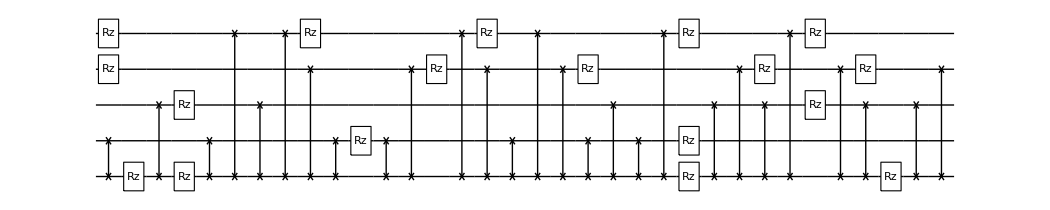

**** Compile @Wed 28 Dec 2022 10:55:09 τ=6.6; δ0.2 ****

τ=6.8; δ=0.2; cost=4.97617×10^-6; ngates=37; runtime=8.29055 min

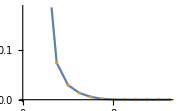

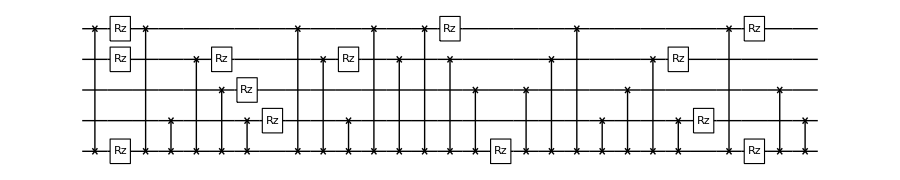

**** Compile @Wed 28 Dec 2022 11:03:32 τ=6.8; δ0.2 ****

τ=7.; δ=0.2; cost=2.04617×10^-6; ngates=41; runtime=12.3255 min

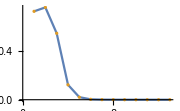

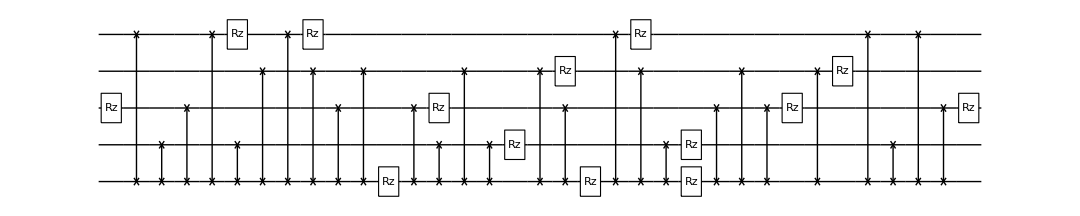

**** Compile @Wed 28 Dec 2022 11:15:58 τ=7.; δ0.2 ****

τ=7.2; δ=0.2; cost=7.27684×10^-6; ngates=45; runtime=6.00345 min

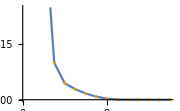

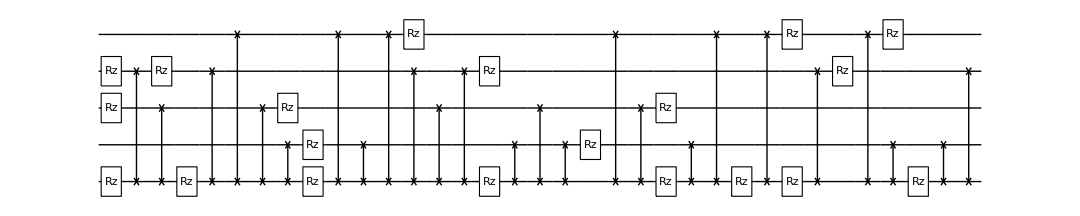

**** Compile @Wed 28 Dec 2022 11:22:04 τ=7.2; δ0.2 ****

τ=7.4; δ=0.2; cost=9.97661×10^-6; ngates=39; runtime=14.2462 min

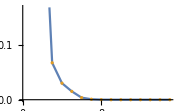

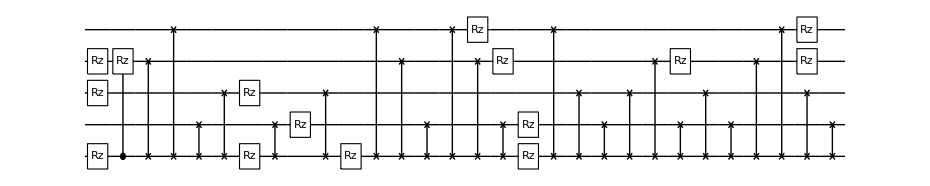

**** Compile @Wed 28 Dec 2022 11:36:25 τ=7.4; δ0.2 ****

τ=7.6; δ=0.2; cost=2.84182×10^-6; ngates=40; runtime=11.9771 min

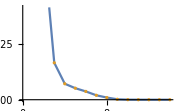

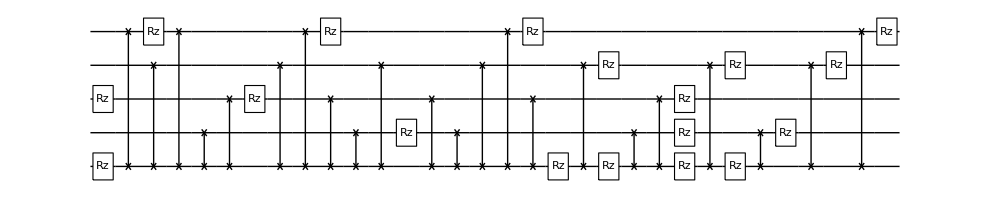

**** Compile @Wed 28 Dec 2022 11:48:30 τ=7.6; δ0.2 ****

τ=7.8; δ=0.2; cost=7.25911×10^-6; ngates=44; runtime=4.3945 min

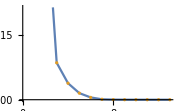

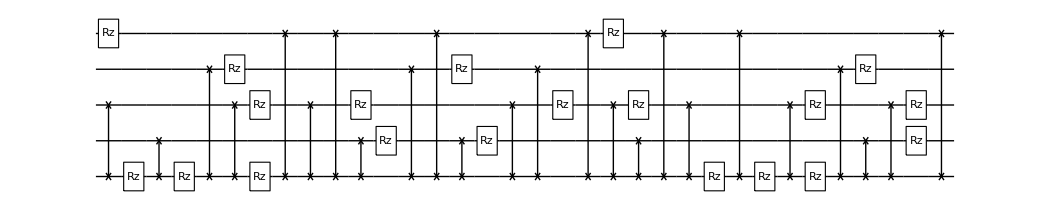

**** Compile @Wed 28 Dec 2022 11:53:00 τ=7.8; δ0.2 ****

τ=8.; δ=0.2; cost=5.27329×10^-6; ngates=38; runtime=8.44811 min

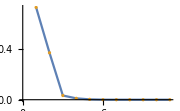

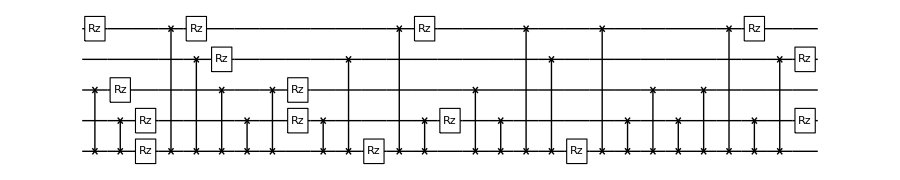

**** Compile @Wed 28 Dec 2022 12:01:33 τ=8.; δ0.2 ****

τ=8.2; δ=0.2; cost=8.48363×10^-6; ngates=44; runtime=14.5504 min

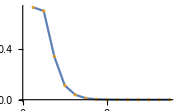

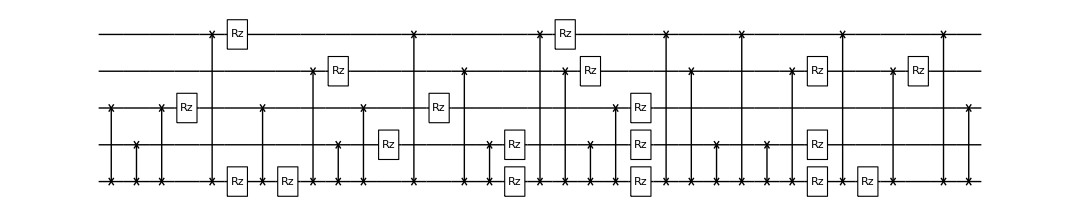

**** Compile @Wed 28 Dec 2022 12:16:12 τ=8.2; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 12:29:40 completed with ngates=40, cost=0.00001290807831721974, at eval=1960

τ=8.4; δ=0.2; cost=8.82601×10^-6; ngates=44; runtime=17.1435 min

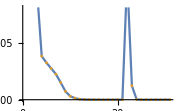

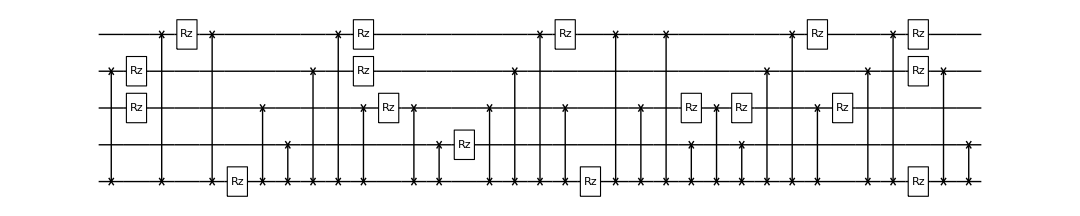

**** Compile @Wed 28 Dec 2022 12:33:26 τ=8.4; δ0.2 ****

τ=8.6; δ=0.2; cost=2.50386×10^-6; ngates=40; runtime=4.57378 min

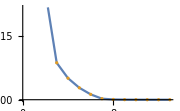

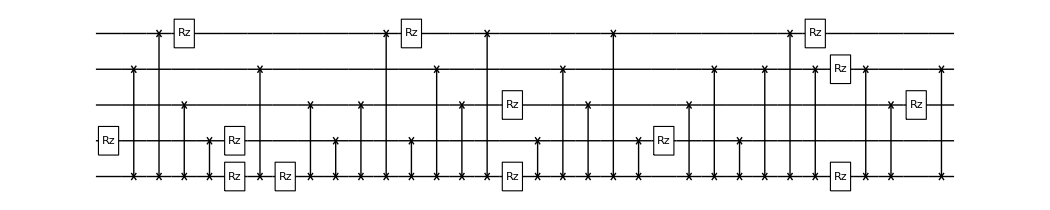

**** Compile @Wed 28 Dec 2022 12:38:07 τ=8.6; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 12:52:36 completed with ngates=34, cost=0.000012214619709238761, at eval=2362

τ=8.8; δ=0.2; cost=4.17183×10^-6; ngates=34; runtime=15.6115 min

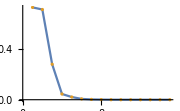

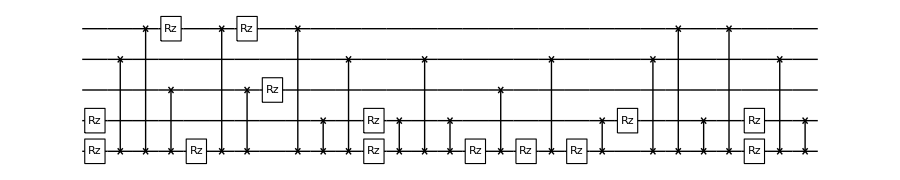

**** Compile @Wed 28 Dec 2022 12:53:50 τ=8.8; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 13:08:18 completed with ngates=40, cost=6.660668159019778e-6, at eval=2279

τ=9.; δ=0.2; cost=4.13255×10^-6; ngates=40; runtime=15.8852 min

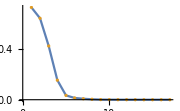

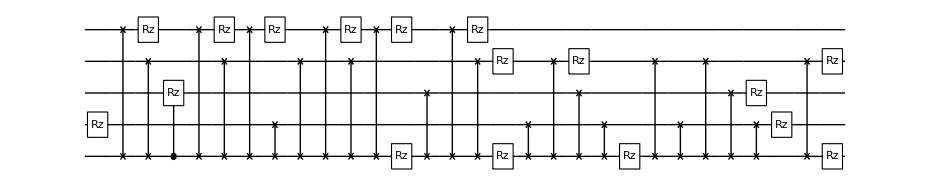

**** Compile @Wed 28 Dec 2022 13:09:49 τ=9.; δ0.2 ****

τ=9.2; δ=0.2; cost=5.94892×10^-6; ngates=49; runtime=5.21094 min

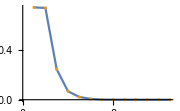

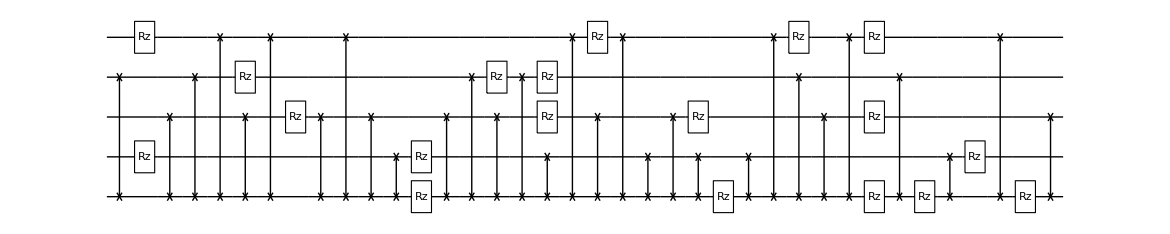

**** Compile @Wed 28 Dec 2022 13:15:08 τ=9.2; δ0.2 ****

τ=9.4; δ=0.2; cost=8.8035×10^-6; ngates=46; runtime=6.91626 min

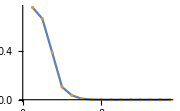

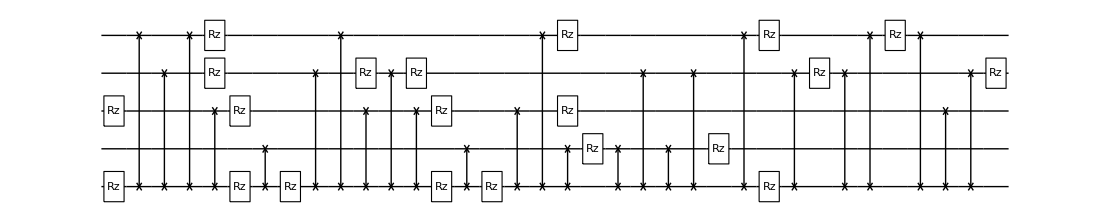

**** Compile @Wed 28 Dec 2022 13:22:09 τ=9.4; δ0.2 ****

τ=9.6; δ=0.2; cost=6.09183×10^-6; ngates=44; runtime=5.01038 min

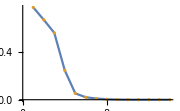

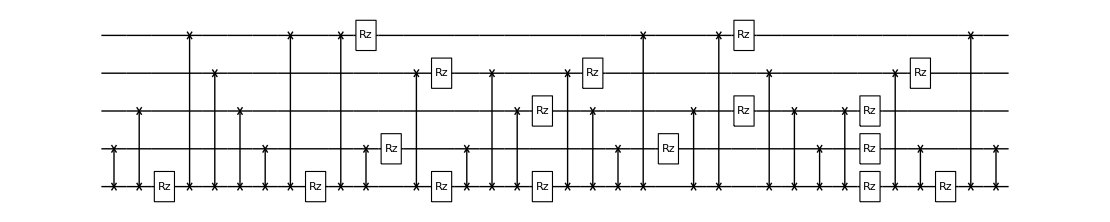

**** Compile @Wed 28 Dec 2022 13:27:15 τ=9.6; δ0.2 ****

τ=9.8; δ=0.2; cost=7.67819×10^-6; ngates=42; runtime=6.61236 min

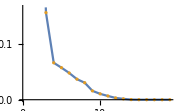

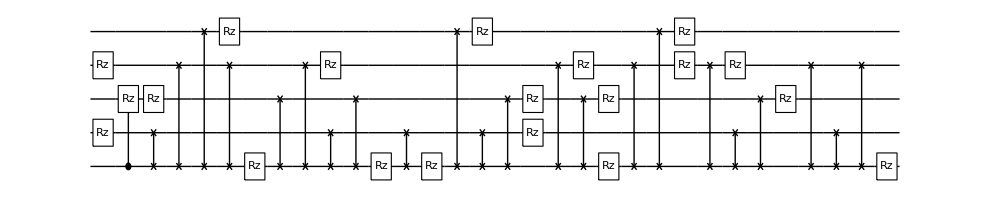

**** Compile @Wed 28 Dec 2022 13:33:58 τ=9.8; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 13:47:19 completed with ngates=38, cost=5.226985851258803e-6, at eval=2148

τ=10.; δ=0.2; cost=1.89572×10^-6; ngates=38; runtime=14.3617 min

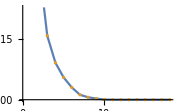

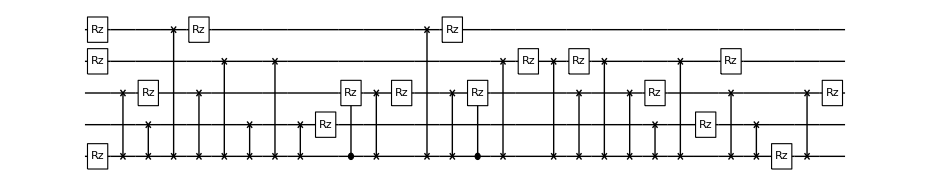

**** Compile @Wed 28 Dec 2022 13:48:26 τ=10.; δ0.2 ****

τ=10.2; δ=0.2; cost=2.82822×10^-6; ngates=38; runtime=7.94329 min

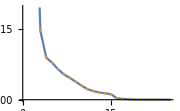

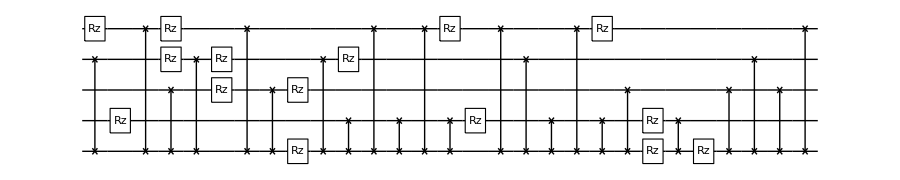

**** Compile @Wed 28 Dec 2022 13:56:29 τ=10.2; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 14:10:28 completed with ngates=43, cost=9.294033720186334e-6, at eval=2090

τ=10.4; δ=0.2; cost=6.72668×10^-6; ngates=43; runtime=15.3973 min

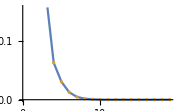

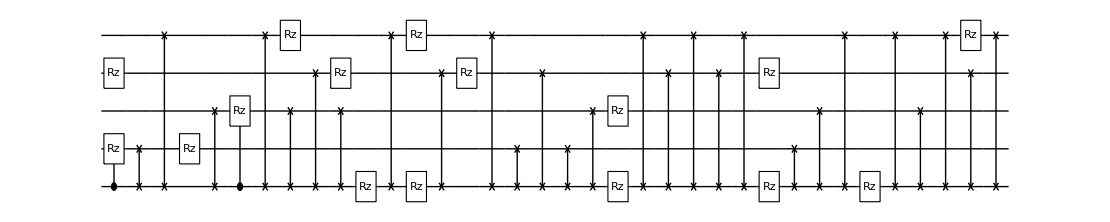

**** Compile @Wed 28 Dec 2022 14:11:59 τ=10.4; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 14:27:14 completed with ngates=35, cost=0.000021810458749715878, at eval=2488

τ=10.6; δ=0.2; cost=9.75458×10^-6; ngates=35; runtime=16.5835 min

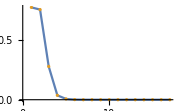

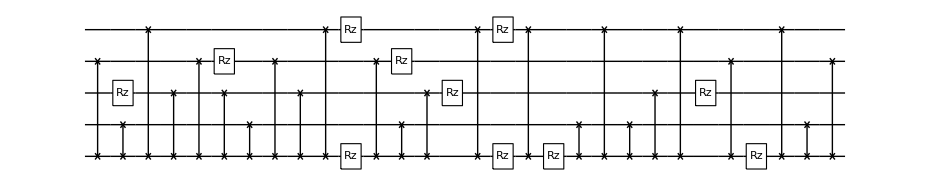

**** Compile @Wed 28 Dec 2022 14:28:40 τ=10.6; δ0.2 ****

τ=10.8; δ=0.2; cost=4.09695×10^-6; ngates=41; runtime=4.97452 min

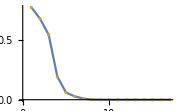

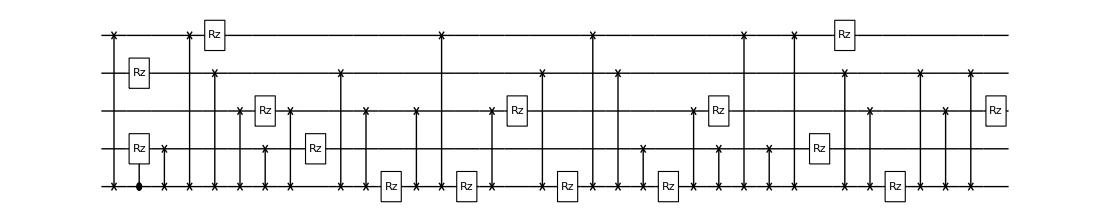

**** Compile @Wed 28 Dec 2022 14:33:44 τ=10.8; δ0.2 ****

τ=11.; δ=0.2; cost=2.25363×10^-6; ngates=36; runtime=4.96251 min

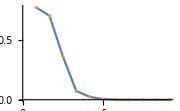

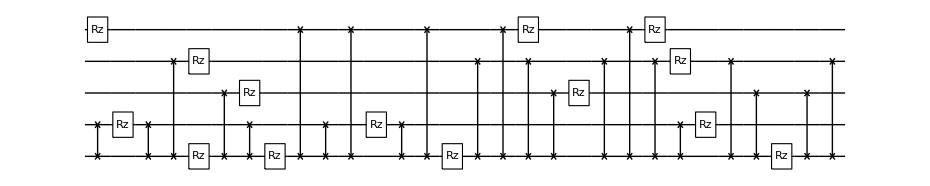

**** Compile @Wed 28 Dec 2022 14:38:48 τ=11.; δ0.2 ****

τ=11.2; δ=0.2; cost=2.74793×10^-6; ngates=45; runtime=9.05366 min

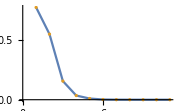

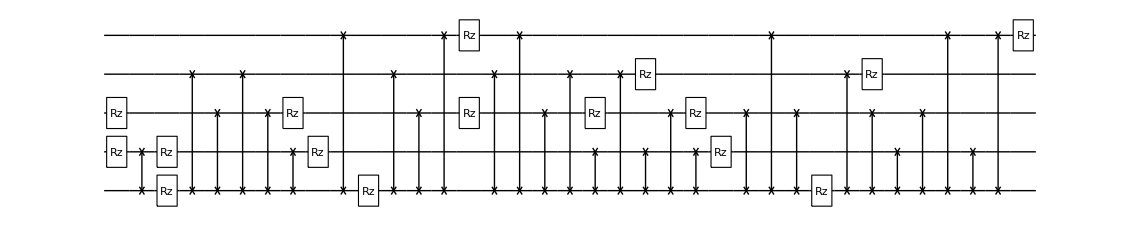

**** Compile @Wed 28 Dec 2022 14:47:58 τ=11.2; δ0.2 ****

τ=11.4; δ=0.2; cost=5.41902×10^-7; ngates=37; runtime=6.12116 min

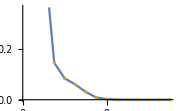

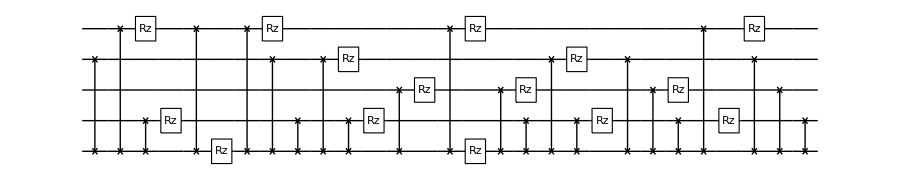

**** Compile @Wed 28 Dec 2022 14:54:11 τ=11.4; δ0.2 ****

τ=11.6; δ=0.2; cost=5.40287×10^-6; ngates=44; runtime=4.35843 min

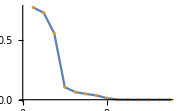

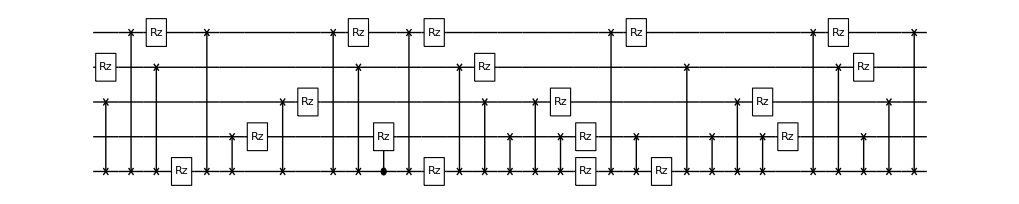

**** Compile @Wed 28 Dec 2022 14:58:34 τ=11.6; δ0.2 ****

τ=11.8; δ=0.2; cost=8.10556×10^-6; ngates=45; runtime=8.84147 min

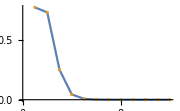

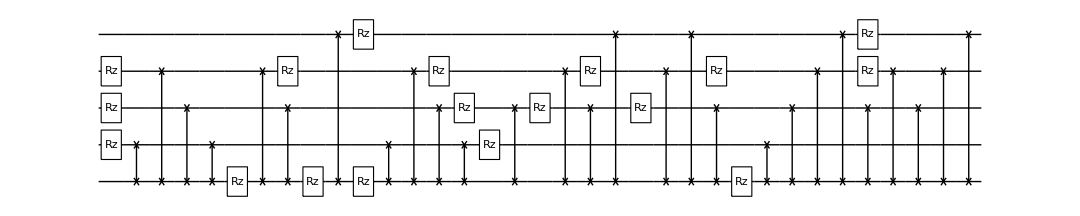

**** Compile @Wed 28 Dec 2022 15:07:31 τ=11.8; δ0.2 ****

τ=12.; δ=0.2; cost=4.23938×10^-6; ngates=40; runtime=5.36187 min

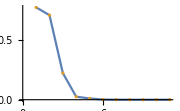

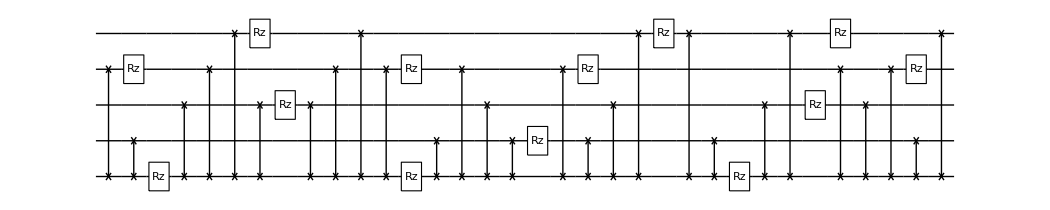

**** Compile @Wed 28 Dec 2022 15:12:58 τ=12.; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 15:26:40 completed with ngates=43, cost=0.00001549830443581257, at eval=2076

τ=12.2; δ=0.2; cost=5.25659×10^-6; ngates=43; runtime=14.9659 min

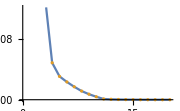

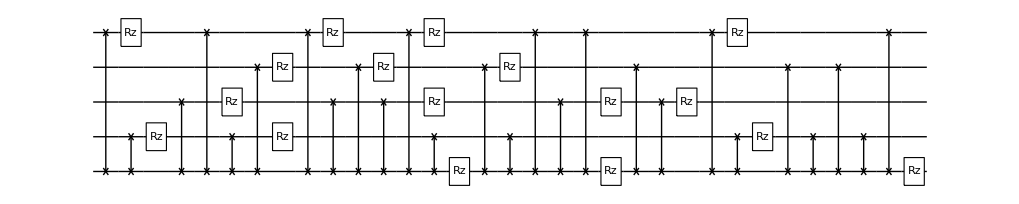

**** Compile @Wed 28 Dec 2022 15:28:03 τ=12.2; δ0.2 ****

τ=12.4; δ=0.2; cost=8.7986×10^-6; ngates=42; runtime=12.8628 min

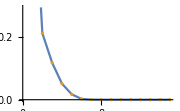

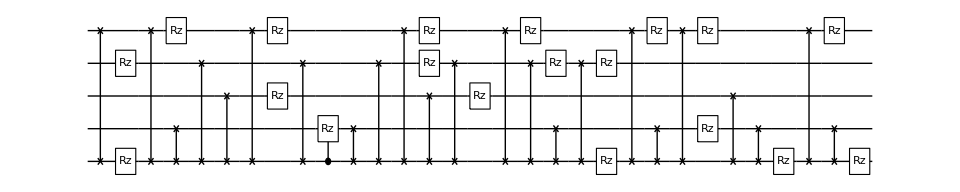

**** Compile @Wed 28 Dec 2022 15:41:00 τ=12.4; δ0.2 ****

τ=12.6; δ=0.2; cost=7.89426×10^-6; ngates=41; runtime=6.50325 min

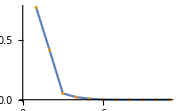

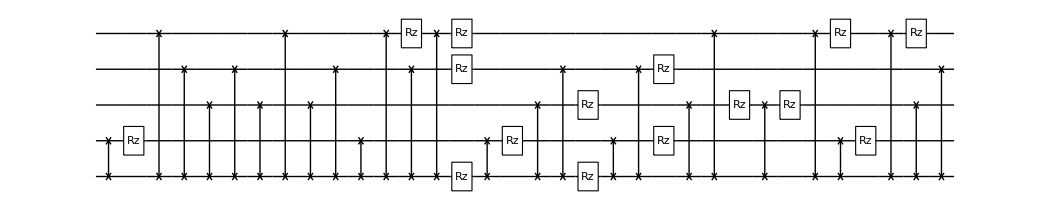

**** Compile @Wed 28 Dec 2022 15:47:37 τ=12.6; δ0.2 ****

τ=12.8; δ=0.2; cost=1.11576×10^-6; ngates=41; runtime=8.87362 min

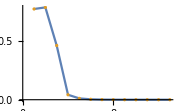

-Graphics-

**** Compile @Wed 28 Dec 2022 15:56:35 τ=12.8; δ0.2 ****

Cycle 1@Wed 28 Dec 2022 16:09:53 completed with ngates=40, cost=0.000015414773279154304, at eval=1985

τ=13.; δ=0.2; cost=5.84017×10^-6; ngates=40; runtime=14.2462 min

-Graphics-

-Graphics-

```mathematica
τ=0.
Table[
Print["**** Compile @",DateString[]," τ=",τ, "; δ",δ," ****"];
hbcsmat=Chop@MatrixExp[-ⅈ *δ*CalcPauliStringMatrix[HBCS[5,ϵ,τ]]]; 
DestroyAllQuregs[];
conf=DefaultConfig[5,{1,2,4,8,16}];
res=CJRecompile[5,hbcsmat,conf];
τ+=δ;
AppendTo[bcscompilecssrerun,{τ,δ,res}];
DumpSave["bcscompilecssrerun.mx",bcscompilecssrerun];
{time,Ecur,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
Print["τ=",τ, "; δ=",δ,"; cost=",Ecur,"; ngates=",Length@ansatz,"; runtime=",time];
Print@ListPlot[{Elist,Elist},Joined->{True,False},ImageSize->Small];
Print@DrawCircuit[ansatz/.CustomGatesDraw,5];
,{i,Length@τs}];
```

The matrixExp vs compiled

```mathematica
(*initialisation*)
{ψexact,ψinitexact}=CreateQuregs[5,2];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

```mathematica
CloneQureg[ψexact,ψinitexact];
rexactcomp={{0,1}};
Table[
{τ,δ,res}=comp;
ApplyCircuit[ψexact,res[[4]]/.CustomGatesDefinitions/.res[[5]]];
AppendTo[rexactcomp,{τ,CalcFidelity[ψexact,ψinitexact]}]
,{comp, bcscompilecss2}];
```

```mathematica
ListPlot[{rexactot2,rexactcomp},Joined->{True,False},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->Large,FrameTicks->{{Range[1,1.55,0.05],None},{Automatic,None}}]
```

-Graphics-